# Clear console

```mathematica
Quiet@Remove["Global`*"]
SetDirectory[NotebookDirectory[]];
```

# Parameters

```mathematica
nmax=177;
var={u,v};
par={a,c,δ};
nvar=Length[var];
fixedpar={δ->(21+√313)/48};
parval={a->1/(16*δ)*(21+√313),c->1/128 (969+37 √313)}/.fixedpar//N;
ηval={ηNF->-0.0919995105221395}//N;
ξval={ξNF->-0.801397527511603}//N;
κval={κNF^2->ⅈ}//N;
C11eval={C11->0.109084591223343*ⅈ}//N;
A3eval={Subscript[ANF, 3]->0.145930074159533-0.00947358642130998*ⅈ}//N;
```

# Equation

```mathematica
kinetics={a-c*u+u^2*v,(c-1)*u-u^2*v};
diffmatrix=DiagonalMatrix[{δ^2,1}];
eq=Solve[kinetics==0,var][[1]];
jacmat=D[kinetics,{var}]/.eq;
kinetics=kinetics/.Table[var[[varnum]]->var[[varnum]]+(var[[varnum]]/.eq),{varnum,nvar}];
```

# Kernel of the Jacobian matrix

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix/.fixedpar;
Tcond2=D[Det[jacobianmat],μNF];
μval=Solve[Tcond2==0,μNF][[1]]/.parval;
ϕNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
];
]
ϕNF[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕNF[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕNF[[submatrixcols]]][[1]];
ϕNF=ϕNF/.ϕsol;
Subscript[sol, 1,1]=Table[Subscript[WNF, 1,1,varnum]->C11*ϕNF[[varnum]],{varnum,nvar}];
```

# Kernel of the adjoint

```mathematica
ψNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
ψNF[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψNF[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψNF[[submatrixrows]]][[1]];
ψNF=ψNF/.ψsol/.fixedpar;
```

# Variables to expand

```mathematica
jacobianmat=jacobianmat/.parval;
jacobianmatr=jacmat-rNF^2*μNF*diffmatrix/.parval/.fixedpar;
ϕNF=ϕNF/.μval/.parval/.C11eval;
ψNF=ψNF/.μval/.parval;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μval/.parval/.C11eval;
negativetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,-nmax,-1}];
positivetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,1,nmax}];
solr1=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
solrn1=LinearSolve[dummymat,dummyvec];
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order]->Sum[Subscript[WNF, order,sub,varnum] ⅇ^(ⅈ sub x)/.Subscript[WNF, order,sub,varnum]->If[sub<0,(-1)^order*ⅇ^(2*sub*ξNF*π)*Conjugate[Subscript[WNF, order,-sub,varnum]]/.ξval,Subscript[WNF, order,sub,varnum]],{sub,-order,order,2}],{order,nmax},{varnum,nvar}]];
toexpand=toexpand/. Subscript[sol, 1,1];
expr=kinetics/.Table[var[[varnum]]->∑_(order=1)^nmax ϵNF^order*Subscript[var[[varnum]], order],{varnum,nvar}]/.parval/.fixedpar;
derivative=D[expr,ϵNF];
```

# Iterative solver

```mathematica
load=1;
SetDirectory[NotebookDirectory[]];
If[FileExistsQ["savedSession.mx"] && load==1,
<<savedSession.mx
,
solvcond={};
ampeval={};
AppendTo[solvcond,0];
]
For[order=If[solvcond=={},2,Length[solvcond]+1],order<=nmax,order++,
save=0;
Print["order="<>ToString[order]];
derivative=D[derivative,ϵNF];
toexpand=toexpand/.ampeval;
equation=1/(order!)*derivative/.ϵNF->0/.toexpand;
equation=Expand[equation]/.negativetab;
If[OddQ[order],
sub=1;
auxeq=1/(2π)∫_0^(2π) equation*ⅇ^(-ⅈ*sub*x)ⅆx;
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]]//Simplify;
If[order>=3,
If[order-2>=sub && OddQ[order],
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=sub && OddQ[order],
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
AppendTo[solvcond,Chop[Simplify[Dot[auxeq,ψNF]/.μval/.fixedpar]]];
If[order>=7 && OddQ[order],
solvcond[[order]]=solvcond[[order]]/.Subscript[ANF, order-2]->0;
If[order==7,
partialsol=A3eval;
,
actualeq=solvcond[[order]];
partialsol=Quiet@NSolve[actualeq==0,Subscript[ANF, order-4],Complexes][[1]];
];
ampeval=Join[ampeval,partialsol];
];
auxeq=auxeq/.ampeval;
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
usefulvec[[submatrixcols]]=Table[Subscript[WNF, order,sub,submatrixcols[[varnum]]]->auxsol[[varnum]]+Subscript[ANF, order]*ϕNF[[submatrixcols[[varnum]]]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[WNF, order,sub,criticalcol]->Subscript[ANF, order]*ϕNF[[criticalcol]];
Subscript[sol, order,sub]=usefulvec/.μval/.C11eval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
,
AppendTo[solvcond,0];
];
For[sub=If[EvenQ[order],0,3],sub<=order,sub+=2,
save=1;
If[sub==0,
auxeq=equation/.positivetab;
,
auxeq=equation/.ⅇ^(ⅈ*sub*x)->1/.positivetab;
];
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]]//Simplify;
If[order>=3,
If[order-2>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
auxsol=solrn1/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.rNF->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}]/.μval/.C11eval;
Subscript[sol, order,sub]=Table[Subscript[WNF, order,sub,varnum]->auxsol[[varnum]],{varnum,nvar}]/.ampeval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
If[sub==0,
equation=equation-(Expand[equation]/.positivetab);
]
];
If[save==1 && sub==order+2,
DumpSave["savedSession.mx",{"Global`","Subscript"}]
]
]
```

order=2

order=3

order=4

order=5

order=6

order=7

order=8

order=9

order=10

order=11

order=12

order=13

order=14

order=15

order=16

order=17

order=18

order=19

order=20

order=21

order=22

order=23

order=24

order=25

order=26

order=27

order=28

order=29

order=30

order=31

order=32

order=33

order=34

order=35

order=36

order=37

order=38

order=39

order=40

order=41

order=42

order=43

order=44

order=45

order=46

order=47

order=48

order=49

order=50

order=51

order=52

order=53

order=54

order=55

order=56

order=57

order=58

order=59

order=60

order=61

order=62

order=63

order=64

order=65

order=66

order=67

order=68

order=69

order=70

order=71

order=72

order=73

order=74

order=75

order=76

order=77

order=78

order=79

order=80

order=81

order=82

order=83

order=84

order=85

order=86

order=87

order=88

order=89

order=90

order=91

order=92

order=93

order=94

order=95

order=96

order=97

order=98

order=99

order=100

order=101

order=102

order=103

order=104

order=105

order=106

order=107

order=108

order=109

order=110

order=111

order=112

order=113

order=114

order=115

order=116

order=117

order=118

order=119

order=120

order=121

order=122

order=123

order=124

order=125

order=126

order=127

order=128

order=129

order=130

order=131

order=132

order=133

order=134

order=135

order=136

order=137

order=138

order=139

order=140

order=141

order=142

order=143

order=144

order=145

order=146

order=147

order=148

order=149

order=150

order=151

order=152

order=153

order=154

order=155

order=156

order=157

order=158

order=159

order=160

order=161

order=162

order=163

order=164

order=165

order=166

order=167

order=168

order=169

order=170

order=171

order=172

order=173

order=174

order=175

order=176

order=177

# Tabulating information

```mathematica
SetDirectory[NotebookDirectory[]];
<<savedSession.mx
PrependTo[ampeval,Subscript[ANF, 1]->C11/.C11eval];
c00tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,0,varnum],{varnum,nvar}]/. Subscript[sol, order,0],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c20tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,2,varnum],{varnum,nvar}]/. Subscript[sol, order,2],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c00tab=Table[{Abs[c00tabaux[[ind]]],Arg[c00tabaux[[ind]]]},{ind,Length[c00tabaux]}];
c00tab[[All,1]]
c20tab=Table[{Abs[c20tabaux[[ind]]],Arg[c20tabaux[[ind]]]},{ind,Length[c20tabaux]}];
c20tab[[All,1]]
```

{0.0986261,0.0244341,0.103479,0.062374,0.0634854,0.0850083,0.0575365,0.0901004,0.0593872,0.0903225,0.0626942,0.0890145,0.0658203,0.0871839,0.0684501,0.0851996,0.0706026,0.0832209,0.0723638,0.0813201,0.0738183,0.0795277,0.0750343,0.0778528,0.076064,0.0762943,0.0769465,0.0748458,0.0777114,0.073499,0.078381,0.0722452,0.0789725,0.0710758,0.0794993,0.0699827,0.0799719,0.0689587,0.0803988,0.0679972,0.0807865,0.0670925,0.0811406,0.0662393,0.0814657,0.065433,0.0817654,0.0646695,0.0820429,0.0639451,0.0823007,0.0632567,0.0825411,0.0626013,0.082766,0.0619763,0.0829769,0.0613794,0.0831754,0.0608085,0.0833626,0.0602617,0.0835396,0.0597373,0.0837073,0.0592337,0.0838665,0.0587496,0.0840179,0.0582837,0.0841623,0.0578348,0.0843,0.0574019,0.0844317,0.0569839,0.0845578,0.0565801,0.0846787,0.0561895,0.0847948,0.0558115,0.0849064,0.0554453,0.0850138,0.0550903}

{0.000957982,0.000209818,0.000245681,0.000295646,0.00023665,0.000254158,0.0002334,0.00024538,0.000237226,0.000246791,0.000242755,0.000250585,0.00024799,0.00025453,0.000252507,0.000258081,0.000256331,0.000261169,0.000259581,0.000263847,0.000262375,0.000266186,0.000264809,0.000268249,0.000266953,0.000270086,0.000268861,0.000271736,0.000270574,0.000273228,0.000272125,0.000274587,0.000273536,0.000275831,0.000274828,0.000276976,0.000276017,0.000278034,0.000277115,0.000279015,0.000278133,0.000279929,0.000279081,0.000280781,0.000279965,0.000281579,0.000280793,0.000282329,0.000281569,0.000283034,0.0002823,0.000283698,0.000282988,0.000284326,0.000283639,0.00028492,0.000284254,0.000285483,0.000284837,0.000286018,0.000285391,0.000286527,0.000285918,0.000287012,0.000286419,0.000287474,0.000286897,0.000287916,0.000287354,0.000288338,0.00028779,0.000288742,0.000288208,0.000289129,0.000288608,0.0002895,0.000288992,0.000289856,0.00028936,0.000290199,0.000289714,0.000290528,0.000290054,0.000290846,0.000290382,0.000291151}

# Plotting

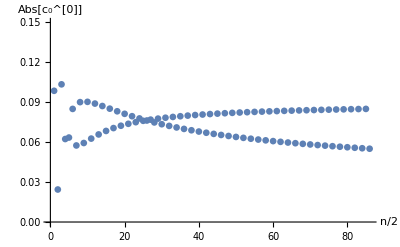

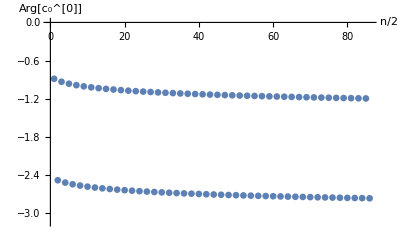

```mathematica
ps=0.012;
c00tabplotabs=ListPlot[Table[{n,c00tab[[n,1]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{0.0,0.15}},AxesLabel->{"n/2","Abs[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c00tabplotangle=ListPlot[Table[{n,c00tab[[n,2]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{-π,0}},AxesLabel->{"n/2","Arg[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

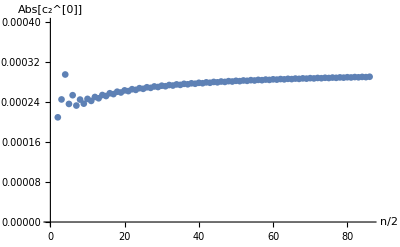

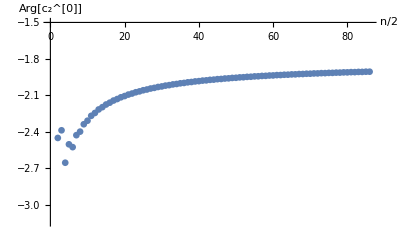

```mathematica
c20tabplotabs=ListPlot[Table[{n,c20tab[[n,1]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{0,0.0004}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c20tabplotangle=ListPlot[Table[{n,c20tab[[n,2]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{-π,-1.5}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

{param_0→0.0382846,param_1→0.839913,param_2→-4.93773}

{param_0→0.0896381,param_1→-0.212353,param_2→0.55678}

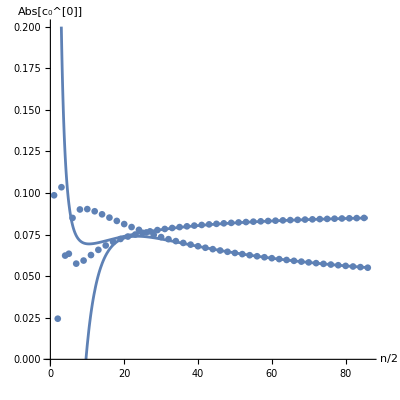

```mathematica
c00funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,1]]},{n,20,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot1=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.2}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,1]]},{n,20,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot2=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.2}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotabs,AxesLabel->{"n/2","Abs[c_0^[0]]"}]
```

```mathematica
(0.038284818698533576+0.08963812596133021)/8
```

0.0159904

{param_0→-2.85708,param_1→4.51738,param_2→-27.1645}

{param_0→-1.28628,param_1→4.56325,param_2→-27.1959}

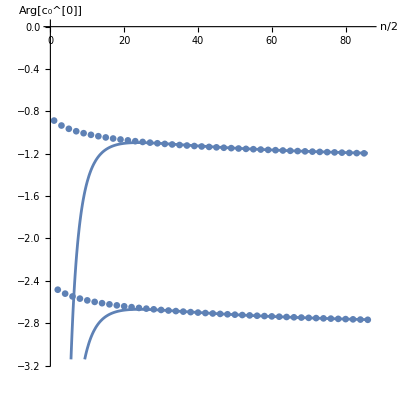

```mathematica
c00funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot1=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-π,0}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot2=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-π,0}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotangle,AxesLabel->{"n/2","Arg[c_0^[0]]"}]
```

{param_0→0.000302335,param_1→-0.00109178,param_2→0.00568479}

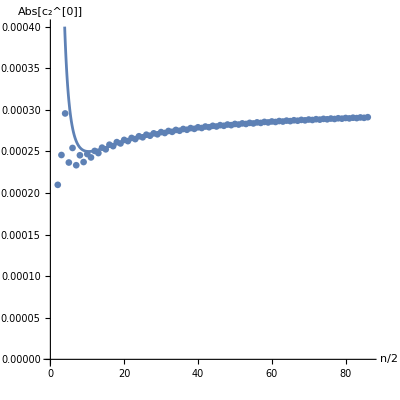

```mathematica
c20funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,1]]},{n,15,Length[c20tab]}],c00funabs,parameters,n]
fitplot=Plot[c20funabs/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{0,0.0004}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotabs]
```

{param_0→-1.83337,param_1→-6.43752,param_2→19.8686}

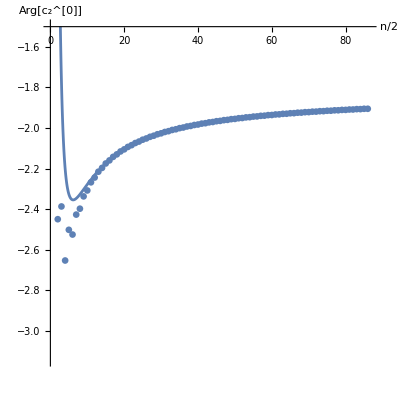

```mathematica
c20funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,2]]},{n,15,Length[c20tab]}],c00funangle,parameters,n]
fitplot=Plot[c20funangle/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{-π,-1.5}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotangle]
```